```mathematica
lisdt=ReadList["~/Lattice/out.txt",Number];
```

```mathematica
lisdt[[1]]
```

0.940213

```mathematica
twopoint=lisdt[[2;;101]];
```

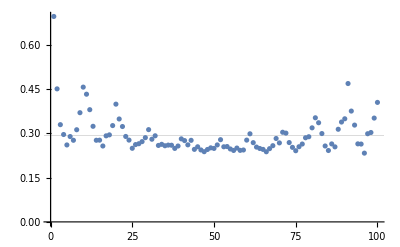

```mathematica
ListPlot[twopoint,PlotRange->Full,GridLines->{{Mean[twopoint]}}]
```

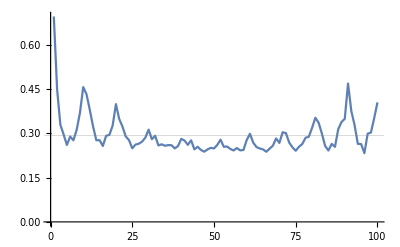

```mathematica
ListLinePlot[twopoint,PlotRange->Full,GridLines->{{Mean[twopoint]}}]
```

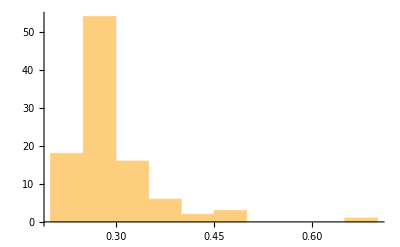

```mathematica
Histogram[twopoint,10]
```

```mathematica
Mean[twopoint]
```

0.293288

```mathematica
momdatarand=Table[{j-k/2,Sum[Flatten[Table[twopoint[[i]],{i,j*k+1,j*k+k}]][[i]]*Exp[(I*Pi/10.)*2*i*0],{i,1,k}]},{j,0,k-1}];
```

```mathematica
p1=Table[Re[ArcCosh[(Transpose[momdatarand][[2]][[i+1]]+Transpose[momdatarand][[2]][[i-1]])/(2*Transpose[momdatarand][[2]][[i]])]],{i,2,9}]
```

{0.178429,0.22652,0.199982,0.226229,0.13404,0.206296,0.147363,0.13536}

```mathematica
Mean[p1]
```

0.181777

```mathematica
lisdt1=ReadList["~/Lattice/out1.txt",Number];
```

```mathematica
twopoint1=lisdt1[[2;;101]];
```

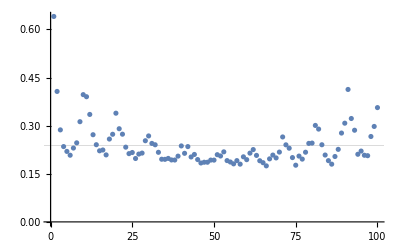

```mathematica
ListPlot[twopoint1,PlotRange->All,GridLines->{{Mean[twopoint1]}}]
```

```mathematica
k=10;
```

```mathematica
momdata1=Re[Table[{j-k/2,Sum[Flatten[Table[twopoint1[[i]],{i,j*k+1,j*k+k}]][[i]]*Exp[(I*Pi/10.)*2*i*6],{i,1,k}]},{j,0,k-1}]]
```

{{-5,-0.150864},{-4,-0.0203906},{-3,0.000710315},{-2,0.0105567},{-1,-0.0105262},{0,-0.00832281},{1,0.0306726},{2,-0.0450769},{3,0.0136603},{4,-0.00231939}}

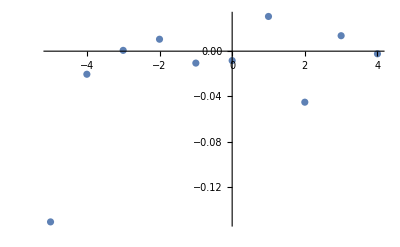

```mathematica
ListPlot[momdata1]
```

```mathematica
p2=Table[Re[ArcCosh[(Transpose[momdata1][[2]][[i+1]]+Transpose[momdata1][[2]][[i-1]])/(2*Transpose[momdata1][[2]][[i]])]],{i,2,9}]
```

{0.739208,0.59039,0.140332,1.913,0.988313,0.620991,0.53454,0.}

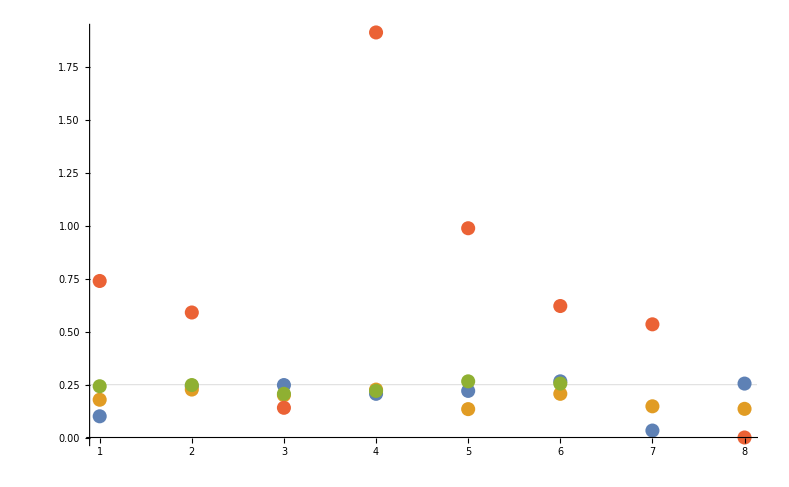

```mathematica
ListPlot[{p,p1,pnew,p2},GridLines->{{.249}},PlotRange->All]
```

```mathematica
Mean[Chop[p,2*10^-1]]
```

0.179502

```mathematica
pnew=DeleteCases[Chop[p,2*10^-1],0];
```